```mathematica
(* 
min z(x1,x2) = 6x1+x2–2
 g1(x1,x2) = 3x1–2x2 ≤ 12
g2(x1,x2) = 2x1+5x2 ≥ –20
g3(x1,x2) = –x1–6x2 ≥ –12
g4(x1,x2) = –x1+2x2 ≤ 4
*)

(* a) 
  g1(x1,x2)= -3x1+2x2 ≥ -12
g2(x1,x2)= 2x1+5x2 ≥ –20
  g3(x1,x2)= –x1–6x2 ≥ –12
  g4(x1,x2)= x1-2x2 ≥ -4
*)

Clear[x1,x2]
g1[x1_,x2_]=-3x1+2x2; 
g2[x1_,x2_]= 2x1+5x2; 
g3[x1_,x2_]= -x1 - 6x2; 
g4[x1_,x2_]=x1-2x2; 

(* define constraint constants *)
b1=-12;
b2=-20;
b3=-12;
b4=-4;

(* define slack var functions to compute slack at any given point (x,y) *)
ss1[x1_,x2_]=g1[x1,x2]-b1;
ss2[x1_,x2_]=g2[x1,x2]-b2;
ss3[x1_,x2_]=g3[x1,x2]-b3;
ss4[x1_,x2_]=g4[x1,x2]-b4;

(* define objective function *)
xx[x1_,x2_]= 6x1 + x2 - 2;

g1[x1_]=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]]
g2[x1_]=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]]
g3[x1_]=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]]
g4[x1_]=x2/.Solve[g4[x1,x2]==b4,{x2}][[1,1]]
```

3/2 (-4+x1)

-2/5 (10+x1)

(12-x1)/6

(4+x1)/2

```mathematica
Plot[{g1[x1],g2[x1],g3[x1],g4[x1]},{x1,-20,40},AspectRatio->Automatic,PlotRange->{{-20,30},{-25,30}},PlotLegends -> "Expressions"]
```

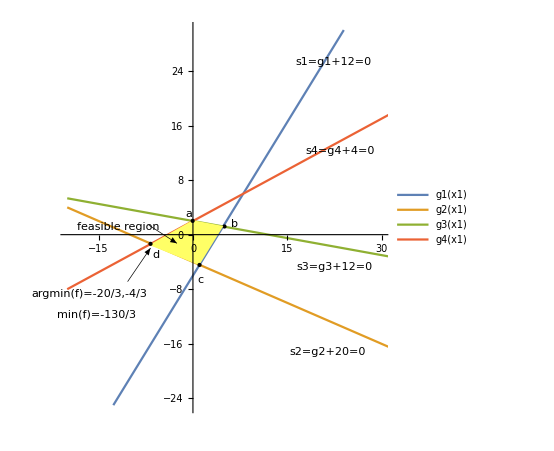

```mathematica
(* Point a *)
(* It is the intersection of S3=0 & S4 = 0 *)
(* y3∇g3 + y4∇g4 = ∇z
y3(-1,-6)+y4(1,-2)= (6,1)
This vector equation is equivalent to the system of equations:
 -y3 + y4  = 6
-6y3 - 2y4 = 1
*)
```

```mathematica
Solve [-y3+y4 == 6 && -6y3-2y4==1,{y3,y4}]
```

{{y3→-13/8,y4→35/8}}

```mathematica
(* Since y3 < 0, Point a is not the minimum. *)
```

```mathematica
(* Point b *)
(* It is the intersection of S1=0 & S3 = 0 *)
(* y1∇g1 + y3∇g3 = ∇z
y1(-3,2)+y3(-1,-6)= (6,1)
This vector equation is equivalent to the system of equations:
-3y1 - y3  = 6 
2y1 - 6y3 = 1
*)
```

```mathematica
Solve [-3y1-y3== 6 && 2y1-6y3==1,{y1,y3}]
```

{{y1→-7/4,y3→-3/4}}

```mathematica
(* Since y1 & y3 < 0, Point b is not the minimum. *)
```

```mathematica
(* Point c *)
(* It is the intersection of S1=0 & S2 = 0 *)
(* y1∇g1 + y2∇g2 = ∇z
y1(-3,2)+y2(2,5)= (6,1)
This vector equation is equivalent to the system of equations:
-3y1 + 2y2  = 6 
2y1 + 5y2 = 1
*)
```

```mathematica
Solve [-3y1 + 2y2== 6 && 2y1 + 5y2==1,{y1,y2}]
```

{{y1→-28/19,y2→15/19}}

```mathematica
(* Since y1 < 0, Point b is not the minimum. *)
```

```mathematica
(* Point d *)
(* It is the intersection of S2=0 & S4 = 0 *)
(* y2∇g2 + y4∇g4 = ∇z
y2(2,5)+y4(1,-2)= (6,1)
This vector equation is equivalent to the system of equations:
 2y2 + y4  = 6 
5y2 - 2y4 = 1
*)
```

```mathematica
Solve [2y2 + y4== 6 && 5y2 - 2y4==1,{y2,y4}]
```

{{y2→13/9,y4→28/9}}

```mathematica
(* Since y2 & y4 ≥ 0, Point d is the minimum. *)
```

```mathematica
(* Since Point d is the intersection of g2=-20 & g4=-4, we can solve the coordinate of Point d. *)
Solve[2x1+5x2==-20 && x1-2x2== -4,{x1,x2}]
```

{{x1→-20/3,x2→-4/3}}

```mathematica
(* The argmin(z) is x1 = -20/3, x2 = -4/3 *)
(* We plug Point D into the z *)
min=6 * -20/3-4/3 -2
```

-130/3

```mathematica
(* min(z)= -130/3 *)
```